# TRS Subproblem Images

We can make pictures of the TRS SubProblem in 2D and 3D
	argmin_(√(p.B.p)≤Δ)g.p+0.5p.A.p
Remember B and A are symmetric n×n matrices and B is positive definite.

### n=2: Saddle

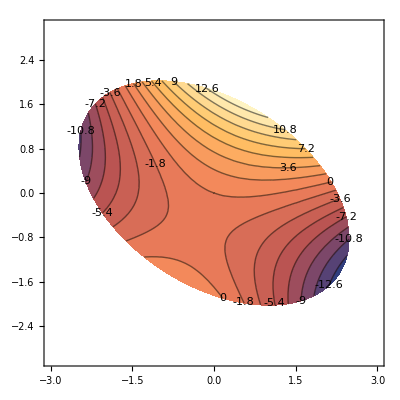

```mathematica
A={{-2.0,3},{3,4}};g={1.2,3.4};
B={{2,1},{1,3}}; Δ=3.2;
f[p_]:=0.5 p.A.p+g.p
ContourPlot[f[{p1,p2}],{p1,-3,3},{p2,-3,3},
Contours->40,
ContourLabels->All,
RegionFunction->Function[{p1,p2},{p1,p2}.B.{p1,p2}≤Δ^2]]
```

### n=2: Interior Max

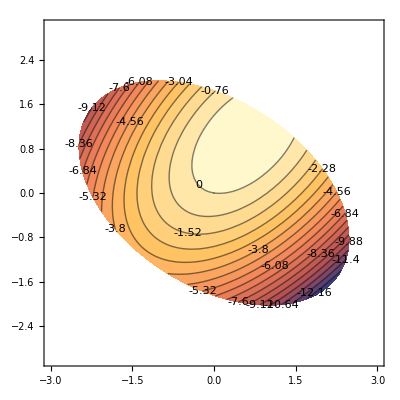

```mathematica
A={{-2.0,1},{1,-2}};g={0.2,1.4};
B={{2,1},{1,3}}; Δ=3.2;
f[p_]:=0.5 p.A.p+g.p
ContourPlot[f[{p1,p2}],{p1,-3,3},{p2,-3,3},
Contours->40,
ContourLabels->All,
RegionFunction->Function[{p1,p2},{p1,p2}.B.{p1,p2}≤Δ^2]]
```

### n=2: Interior Min

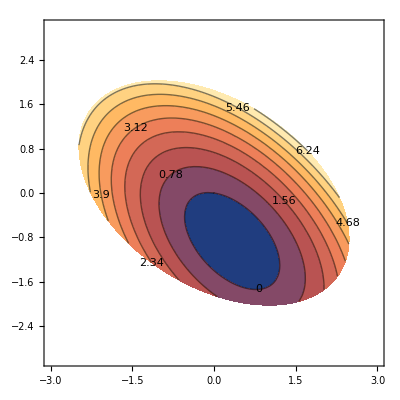

```mathematica
A={{2.0,1},{1,2}};g={0.2,1.4};
B={{2,1},{1,3}}; Δ=3.2;
f[p_]:=0.5 p.A.p+g.p
ContourPlot[f[{p1,p2}],{p1,-3,3},{p2,-3,3},
Contours->40,
ContourLabels->All,
RegionFunction->Function[{p1,p2},{p1,p2}.B.{p1,p2}≤Δ^2]]
```